# Split Expression

This notebook will look at doing a split-expression system with the Protease bait model. We shouldn’t have to change parameters, but we will have to lose the radial symmetry. So we will need to set up partial differential equations with 2 spatial variables rather than just 1.

# Model Equations: No Split

Set up the 2 + 1 D equations, but keep the system the same as before just to make sure we get the same results with the same parameters

```mathematica
rd=10.;(* μm. spatial scale.*)
t0=47; (*s. median time for 2nd expansion signal to start from Erica's paper. *)
DL=260; (*μm^2/s. Estimated free diffusion constant of GBP*)
LRth =.5; (*Dimensionless. Ratio of [L.R] Subscript[to [R], T] needed for signal to be "on"*)
dr=.001; (*"small" r since we cannot use the origin in polar coordinates, μm*)
ρFar=1000/rd (*r that is "infinity" for numeric solving. scaled*);

condrFarx=DirichletCondition[x[r,θ,t]==0.,r==ρFar&&0<θ≤2*π];
condrFarz=DirichletCondition[z[r,θ,t]==0.,r==ρFar&&0<θ≤2*π];

periodx=PeriodicBoundaryCondition[x[r,θ,t],θ==0.,TranslationTransform[{0.,2*π}]];
(*periodyT=PeriodicBoundaryCondition[yT[r,θ,t],θ==0.,TranslationTransform[{0.,2*π}]];*)
periodz=PeriodicBoundaryCondition[z[r,θ,t],θ==0.,TranslationTransform[{0.,2*π}]];


(*Differential Equations*)
s=γd/γw^2*Exp[-(r-dr)^2/(2*γw^2)-γd*t];

dx=D[x[r,θ,t],t]-(1+(γpL*yT[r,θ,t])/(1+γP*x[r,θ,t])^2)^-1*(γDP*Laplacian[x[r,θ,t],{r,θ},"Polar"]+s+γc*γpL/γP*((γP*x[r,θ,t])/(1+γP*x[r,θ,t]))^2*yT[r,θ,t])==condrFarx;

dyT=D[yT[r,θ,t],t]==(-γc*γP*x[r,θ,t]*yT[r,θ,t])/(1+γP*x[r,θ,t]);

dz=D[z[r,θ,t],t]-(1+γR/(1+γL*z[r,θ,t])^2)^-1*(γDL*Laplacian[z[r,θ,t],{r,θ},"Polar"]+(γc*γP*x[r,θ,t]*yT[r,θ,t])/(1+γP*x[r,θ,t]))==condrFarz;

(*Initial Conditions and Boundary Conditions*)
initx=x[r,θ,0]==0.; (*Initially no active protease*)

inityT=yT[r,θ,0]==1.; (*proligand initially exists at all points in space*)

initz=z[r,θ,0]==0; (*Initially no ligand*)


deqns={dx,dyT,dz,initx,inityT,initz,periodx,(*periodyT,*)periodz};
```

# Data

```mathematica
(*secondExpansionData is a list of elements for each data set {calcium radius at all times, calcium radius during second expansion, wound sizes*)
{dataAll,data2ndExp,woundSizes}=Transpose[Import["C:\\Users\\Greg Stevens\\Dropbox\\Research_Backup\\CurrentWork\\LigandModel\\Reviewer3\\SecondExpansionData.m"][[{1,15,17,19,20}]]];
scaledData=data2ndExp/.{t_?NumericQ,r_?NumericQ}->{t/t0,r/rd};

(*Add to data extra points for fitting*)
maxRads=MaximalBy[#,Last][[1,2]]&/@scaledData;
Δt=(#[[2,1]]-#[[1,1]])&/@scaledData;
scaledDataFitting=Table[Join[scaledData[[set]],Table[{scaledData[[set,-1,1]]+i*Δt[[set]],maxRads[[set]]},{i,Length@scaledData[[set]]}]],{set,Length@scaledData}];

(*Set max time to just be a little past this final data point. No need to go farther in time for fitting. Can look at farther time if inspecting particular parameter sets*)
τmaxes=(1.1*#[[;;,1]]//Last)&/@scaledDataFitting;
times=scaledDataFitting[[;;,;;,1]];(*Only need to pick out time points corresponding to the data*)
```

```mathematica
scaledDataAll=dataAll/.{t_?NumericQ,r_?NumericQ}->{t/t0,r/rd};
```

## Import Best Fit parameters

### Pre-χ test

```mathematica
fitsTrial1=Table[(Import/@FileNames["C:\\Users\\Greg Stevens\\Dropbox\\Research_Backup\\CurrentWork\\LigandModel\\Reviewer3\\Fits to Five Sets\\Individual Fits\\set"<>ToString[set]<>"\\Analysis\\fit*.m"])[[;;,1]],{set,{1,15,17,19,20}}];
```

```mathematica
fitsTrial2=Table[Import/@FileNames["C:\\Users\\Greg Stevens\\Dropbox\\Research_Backup\\CurrentWork\\LigandModel\\Reviewer3\\Fits to Five Sets\\Individual Fits\\betterInits\\NLMF\\set"<>ToString[set]<>"\\analysis\\bestParams*.m"],{set,{1,15,17,19,20}}];

fitsTrial3=Table[Import/@FileNames["C:\\Users\\Greg Stevens\\Dropbox\\Research_Backup\\CurrentWork\\LigandModel\\Reviewer3\\Fits to Five Sets\\Individual Fits\\NLMF with Best Fits\\set"<>ToString[set]<>"\\bestParams*.m"],{set,{1,15,17,19,20}}];
```

```mathematica
fitParameters=DeleteDuplicates[#,Round[#1,.001]==Round[#2,.001]&]&/@Table[Join[fitsTrial1[[set]],fitsTrial2[[set]],fitsTrial3[[set]]],{set,Length@scaledDataFitting}];
```

### post χ test

This is done in the main LR analysis notebook

```mathematica
lrparams=Import["C:\\Users\\Greg Stevens\\Dropbox\\Research_Backup\\CurrentWork\\LigandModel\\Reviewer3\\LRParams.m"];
```

# Some Functions

### Get / Undo Parameters

```mathematica
getParams[{ΓDP_,ΓDL_,Γd_,Γc_,ΓP_,ΓpL_,ΓL_,ΓR_,Γw_}]:=
{
γDP->12.22*10^#[[1]] ,(*Estimated from scales and DP 12.22 ≈ .1DL*)
γDL->t0/rd^2*DL*#[[2]], (*known value*)
γd->10^#[[3]] ,
γc->10^#[[4]],
γP->10^#[[5]],
γpL->10^#[[6]],
γL->10^#[[7]],
γR->10^#[[8]],
γw->#[[9]]
}&[{ΓDP,ΓDL,Γd,Γc,ΓP,ΓpL,ΓL,ΓR,Γw}];

undoParams[rules_]:=
{
Log[10,γDP/12.22],
rd^2/(t0*DL)*γDL,
Log[10,γd],
Log[10,γc],
Log[10,γP],
Log[10,γpL],
Log[10,γL],
Log[10,γR],
γw
}/.rules;
```

## Check if radially symmetric version matches 2+1D model with radially symmetric initial / boundary conditions

### Mesh

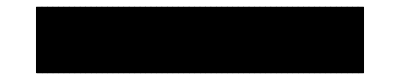

```mathematica
Needs["NDSolve`FEM`"]

nGrid=60.;

coords=Table[{r,θ},{θ,0,2*π,2*π/nGrid},{r,dr,ρFar,(ρFar-dr)/nGrid}]//Flatten[#,1]&;

elems=Table[If[Mod[a,nGrid+1]==0,Nothing,{a,a+1,a+nGrid+2,a+nGrid+1}],{a,Length@coords-(nGrid+2)}];

meshD=ToElementMesh["Coordinates"->coords,"MeshElements"->{QuadElement[elems]}];

meshD["Wireframe"]
```

### 2 + 1 D Model Output

```mathematica
paramsTest=lrparams[[1,2]]
(*paramsTest=lrparams[[2,2]]*)
```

{γDP→0.001222,γDL→134.42,γd→2.20039,γc→0.484172,γP→237.137,γpL→0.006346,γL→9.01571,γR→0.266073,γw→5.}

```mathematica
(*solnTest=NDSolveValue[deqns/.paramsTest,z,{r,dr,ρFar},{θ,0.,2*π},{t,0,τmaxes[[1]]},Method->{"IndexReduction"->Automatic,"EquationSimplification"->"Residual"}];*)
solnTest=NDSolveValue[deqns/.paramsTest,z,{r,θ}∈meshD,{t,0,τmaxes[[1]]},Method->{"IndexReduction"->Automatic,"EquationSimplification"->"Residual"},AccuracyGoal->1,PrecisionGoal->1];
```

```mathematica
Manipulate[Plot[((γL*solnTest[r,θ,t])/(1+γL*solnTest[r,θ,t]))/.paramsTest,{r,dr,15.},PlotRange->{0,1}],{t,0.,3.5},{θ,0.,2*π,π/10}]
```

ReplaceAll::reps: {paramsTest} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

### 1+1D Model

```mathematica
rd=10.;(* μm. spatial scale.*)
t0=47; (*s. median time for 2nd expansion signal to start from Erica's paper. *)
DL=260; (*μm^2/s. Estimated free diffusion constant of GBP*)
LRth =.5; (*Dimensionless. Ratio of [L.R] Subscript[to [R], T] needed for signal to be "on"*)
dr=.001; (*"small" r since we cannot use the origin in polar coordinates, μm*)
ρFar=1000/rd (*r that is "infinity" for numeric solving. scaled*);

(*Differential Equations*)
s=γd/γw^2*Exp[-(r-dr)^2/(2*γw^2)-γd*t];
dx=D[x[r,t],t]==(1+(γpL*yT[r,t])/(1+γP*x[r,t])^2)^-1*(γDP*Laplacian[x[r,t],{r,θ},"Polar"]+s+γc*γpL/γP*((γP*x[r,t])/(1+γP*x[r,t]))^2*yT[r,t]);
dyT=D[yT[r,t],t]==(-γc*γP*x[r,t]*yT[r,t])/(1+γP*x[r,t]);
dz=D[z[r,t],t]==(1+γR/(1+γL*z[r,t])^2)^-1*(γDL*Laplacian[z[r,t],{r,θ},"Polar"]+(γc*γP*x[r,t]*yT[r,t])/(1+γP*x[r,t]));

(*Initial Conditions and Boundary Conditions*)
initx=x[r,0]==0.; (*Initially no active protease*)
bc1x=(D[x[r,t],r]==0)/.r->dr; (*Radially symmetric --> no flux through origin*)
bc2x=x[ρFar,t]==0.; (*Concentration to 0 far away*)

inityT=yT[r,0]==1.; (*proligand initially exists at all points in space*)

initz=z[r,0]==0; (*Initially no ligand*)
bc1z=(D[z[r,t],r]==0)/.r->dr; (*Radially symmetric --> no flux through origin*)
bc2z=z[ρFar,t]==0.; (*Concentration to 0 far away*)

(*Put it all together*)
deqnsXY={dx,dyT,initx,bc1x,bc2x,inityT};
deqnsZ={dz,initz,bc1z,bc2z};
deqns=Join[deqnsXY,deqnsZ];

solnTestOld=soln=NDSolveValue[deqns/.paramsTest,z,{r,dr,ρFar},{t,0,τmaxes[[1]]},Method->{"IndexReduction"->Automatic,"EquationSimplification"->"Residual","PDEDiscretization"->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid","MinPoints"->200,"MaxPoints"->500,"DifferenceOrder"->2}}}];
```

```mathematica
Manipulate[Plot[{((γL*solnTest[r,θ,t])/(1+γL*solnTest[r,θ,t]))/.paramsTest,(γL*solnTestOld[r,t])/(1+γL*solnTestOld[r,t])/.paramsTest},{r,dr,15.},PlotRange->{0,1}],{t,0.,3.5},{θ,0.,2*π,π/10}]
```

# Split Expression GBP

```mathematica
rd=10.;(* μm. spatial scale.*)
t0=47; (*s. median time for 2nd expansion signal to start from Erica's paper. *)
DL=260; (*μm^2/s. Estimated free diffusion constant of GBP*)
LRth =.5; (*Dimensionless. Ratio of [L.R] Subscript[to [R], T] needed for signal to be "on"*)
dr=.001; (*"small" r since we cannot use the origin in polar coordinates, μm*)
ρFar=1000/rd (*r that is "infinity" for numeric solving. scaled*);

condrFarx=DirichletCondition[x[r,θ,t]==0.,r==ρFar&&0<θ≤2*π];
condrFarz=DirichletCondition[z[r,θ,t]==0.,r==ρFar&&0<θ≤2*π];

periodx=PeriodicBoundaryCondition[x[r,θ,t],θ==0.,TranslationTransform[{0.,2*π}]];
periodyT=PeriodicBoundaryCondition[yT[r,θ,t],θ==0.,TranslationTransform[{0.,2*π}]];
periodz=PeriodicBoundaryCondition[z[r,θ,t],θ==0.,TranslationTransform[{0.,2*π}]];


(*Differential Equations*)
s=γd/γw^2*Exp[-(r-dr)^2/(2*γw^2)-γd*t];

dx=D[x[r,θ,t],t]-(1+(γpL*yT[r,θ,t])/(1+γP*x[r,θ,t])^2)^-1*(γDP*Laplacian[x[r,θ,t],{r,θ},"Polar"]+s+γc*γpL/γP*((γP*x[r,θ,t])/(1+γP*x[r,θ,t]))^2*yT[r,θ,t])==condrFarx;

dyT=D[yT[r,θ,t],t]==(-γc*γP*x[r,θ,t]*yT[r,θ,t])/(1+γP*x[r,θ,t]);

dz=D[z[r,θ,t],t]-(1+γR/(1+γL*z[r,θ,t])^2)^-1*(γDL*Laplacian[z[r,θ,t],{r,θ},"Polar"]+(γc*γP*x[r,θ,t]*yT[r,θ,t])/(1+γP*x[r,θ,t]))==condrFarz;

(*Initial Conditions and Boundary Conditions*)
initx=x[r,θ,0]==0.; (*Initially no active protease*)

(*inityT=yT[r,θ,0]==Piecewise[{{1.,0<θ≤π},{0.,π<θ≤2.*π}}];*) (*proligand initially exists only in one half of the plane*)
(*inityT=yT[r,θ,0]==Piecewise[{{1.,0<θ≤π/2.||3.*π/2<θ≤2*π},{0.,π/2.<θ≤3.*π/2.}}];*)
inityT=yT[r,θ,0]==If[π/2.<θ≤3.*π/2.,0.,1.];

initz=z[r,θ,0]==0; (*Initially no ligand*)


deqns={dx,dyT,dz,initx,inityT,initz,periodx,(*periodyT,*)periodz};
```

### Mesh

```mathematica
Needs["NDSolve`FEM`"]

nGrid=60.;

coords=Table[{r,θ},{θ,0,2*π,2*π/nGrid},{r,dr,ρFar,(ρFar-dr)/nGrid}]//Flatten[#,1]&;

elems=Table[If[Mod[a,nGrid+1]==0,Nothing,{a,a+1,a+nGrid+2,a+nGrid+1}],{a,Length@coords-(nGrid+2)}];

meshD=ToElementMesh["Coordinates"->coords,"MeshElements"->{QuadElement[elems]}];

meshD["Wireframe"]
```

-Graphics-

### Solution Test

```mathematica
(*paramsSplit=getParams@fitParameters[[1,1]]*)
paramsSplit=lrparams[[1,2]]
```

{γDP→0.001222,γDL→134.42,γd→2.20039,γc→0.484172,γP→237.137,γpL→0.006346,γL→9.01571,γR→0.266073,γw→5.}

```mathematica
(*solnSplit=NDSolveValue[deqns/.paramsSplit,z,{r,dr,ρFar},{θ,0.,2*π},{t,0,τmaxes[[1]]},Method->{"IndexReduction"->Automatic,"EquationSimplification"->"Residual"}];*)
solnSplitgbp=NDSolveValue[deqns/.paramsSplit,z,{r,θ}∈meshD,{t,0,τmaxes[[1]]},Method->{"IndexReduction"->Automatic,"EquationSimplification"->"Residual"}];
```

```mathematica
Manipulate[Plot[{((γL*solnTest[r,θ,t])/(1+γL*solnTest[r,θ,t]))/.paramsTest,((γL*solnSplitgbp[r,θ,t])/(1+γL*solnSplitgbp[r,θ,t]))/.paramsSplit},{r,dr,15.},PlotRange->{0,1},AxesLabel->{"r (scaled)","[LR]/[R]_T"}],{t,0.,3.5},{θ,0.,2*π,π/10}]
```

```mathematica
Manipulate[
Plot[
{
((γL*solnTest[r/rd,0.,t])/(1+γL*solnTest[r/rd,0.,t]))/.paramsTest,
((γL*solnSplitgbp[r/rd,0.,t])/(1+γL*solnSplitgbp[r/rd,0.,t]))/.paramsSplit,
((γL*solnSplitgbp[r/rd,π/2,t])/(1+γL*solnSplitgbp[r/rd,π/2,t]))/.paramsSplit,
((γL*solnSplitgbp[r/rd,π,t])/(1+γL*solnSplitgbp[r/rd,π,t]))/.paramsSplit
},
{r,dr*rd,15.*rd},
PlotRange->{0,.7},
AxesLabel->{"r (μm)","[LR]/[R]_T"},
PlotLegends->{"Control System","GBP Side","Boundary","No GBP Side"}]
,{t,0.,3.5}]
```

```mathematica
getAngle[x_,y_]:=If[
{x,y},

x==0&&y≥0,π/2.,
If[
x==0&&y<0,3*π/2.,
If[
x>0&&y≥0,ArcTan[y/x],
If[
x<0,π+ArcTan[y/x],
If[
x>0&&y<0,3*π/2-ArcTan[y/x]
]]]]]
```

```mathematica
Manipulate[Plot3D[((γL*solnSplitgbp[Sqrt[x^2+y^2],getAngle[x,y],t])/(1+γL*solnSplitgbp[Sqrt[x^2+y^2],getAngle[x,y],t]))/.paramsSplit,{x,-15,15},{y,-15,15},PlotRange->{-.0001,.7}],{t,0.,3.}]
```

# Split Expression Mthl10

```mathematica
rd=10.;(* μm. spatial scale.*)
t0=47; (*s. median time for 2nd expansion signal to start from Erica's paper. *)
DL=260; (*μm^2/s. Estimated free diffusion constant of GBP*)
LRth =.5; (*Dimensionless. Ratio of [L.R] Subscript[to [R], T] needed for signal to be "on"*)
dr=.001; (*"small" r since we cannot use the origin in polar coordinates, μm*)
ρFar=1000/rd (*r that is "infinity" for numeric solving. scaled*);

condrFarx=DirichletCondition[x[r,θ,t]==0.,r==ρFar&&0<θ≤2*π];
condrFarz=DirichletCondition[z[r,θ,t]==0.,r==ρFar&&0<θ≤2*π];

periodx=PeriodicBoundaryCondition[x[r,θ,t],θ==0.,TranslationTransform[{0.,2*π}]];
periodyT=PeriodicBoundaryCondition[yT[r,θ,t],θ==0.,TranslationTransform[{0.,2*π}]];
periodz=PeriodicBoundaryCondition[z[r,θ,t],θ==0.,TranslationTransform[{0.,2*π}]];


(*Differential Equations*)
s=γd/γw^2*Exp[-(r-dr)^2/(2*γw^2)-γd*t];

dx=D[x[r,θ,t],t]-(1+(γpL*yT[r,θ,t])/(1+γP*x[r,θ,t])^2)^-1*(γDP*Laplacian[x[r,θ,t],{r,θ},"Polar"]+s+γc*γpL/γP*((γP*x[r,θ,t])/(1+γP*x[r,θ,t]))^2*yT[r,θ,t])==condrFarx;

dyT=D[yT[r,θ,t],t]==(-γc*γP*x[r,θ,t]*yT[r,θ,t])/(1+γP*x[r,θ,t]);

dz=D[z[r,θ,t],t]-(1+γR*If[π/2.<θ≤3.*π/2.,.3,1.]/(1+γL*z[r,θ,t])^2)^-1*(γDL*Laplacian[z[r,θ,t],{r,θ},"Polar"]+(γc*γP*x[r,θ,t]*yT[r,θ,t])/(1+γP*x[r,θ,t]))==condrFarz;

(*Initial Conditions and Boundary Conditions*)
initx=x[r,θ,0]==0.; (*Initially no active protease*)

inityT=yT[r,θ,0]==1.;

initz=z[r,θ,0]==0; (*Initially no ligand*)


deqns={dx,dyT,dz,initx,inityT,initz,periodx,(*periodyT,*)periodz};
```

### Mesh

```mathematica
Needs["NDSolve`FEM`"]

nGrid=60.;

coords=Table[{r,θ},{θ,0,2*π,2*π/nGrid},{r,dr,ρFar,(ρFar-dr)/nGrid}]//Flatten[#,1]&;

elems=Table[If[Mod[a,nGrid+1]==0,Nothing,{a,a+1,a+nGrid+2,a+nGrid+1}],{a,Length@coords-(nGrid+2)}];

meshD=ToElementMesh["Coordinates"->coords,"MeshElements"->{QuadElement[elems]}];

meshD["Wireframe"]
```

-Graphics-

### Solution Test

```mathematica
paramsSplit=lrparams[[1,2]]
```

{γDP→0.001222,γDL→134.42,γd→2.20039,γc→0.484172,γP→237.137,γpL→0.006346,γL→9.01571,γR→0.266073,γw→5.}

```mathematica
(*solnSplit=NDSolveValue[deqns/.paramsSplit,z,{r,dr,ρFar},{θ,0.,2*π},{t,0,τmaxes[[1]]},Method->{"IndexReduction"->Automatic,"EquationSimplification"->"Residual"}];*)
solnSplit=NDSolveValue[deqns/.paramsSplit,z,{r,θ}∈meshD,{t,0,τmaxes[[1]]},Method->{"IndexReduction"->Automatic,"EquationSimplification"->"Residual"}];
```

```mathematica
Manipulate[Plot[{(*((γL*solnTest[r,θ,t])/(1+γL*solnTest[r,θ,t]))/.paramsTest,*)If[π/2.<θ≤3.*π/2.,.5,1.]*((γL*solnSplit[r,θ,t])/(1+γL*solnSplit[r,θ,t]))/.paramsSplit},{r,dr,15.},PlotRange->{0,.7},AxesLabel->{"r (scaled)","[LR]/[R]_T"}],{t,0.,3.5},{θ,0.,2*π,π/10}]
```

```mathematica
Manipulate[Plot[
{
(*((γL*solnTest[r/rd,0.,t])/(1+γL*solnTest[r/rd,0.,t]))/.paramsTest,*)
((γL*solnSplit[r/rd,0.,t])/(1+γL*solnSplit[r/rd,0.,t]))/.paramsSplit,
.75*((γL*solnSplit[r/rd,π,t])/(1+γL*solnSplit[r/rd,π,t]))/.paramsSplit
},
{r,dr*rd,15.*rd},
PlotRange->{0,.7},
AxesLabel->{"r (scaled)","[LR]/[R]_T"},
PlotLegends->{"Control System","Mthl10 Side","Reduced Mthl10 Side"}],
{{t,1.35},0.,3.5}]
```

```mathematica
Plot[Evaluate@Table[(γL*solnSplit[r/rd,0.,t])/(1+γL*solnSplit[r/rd,0.,t])/.paramsSplit,{t,0,3.5,3.5/10}],{r,dr*rd,30*rd},
PlotLabels->Table[Round[τ*t0,1],{τ,0,3.5,3.5/10}],
AspectRatio->1,
PlotRange->{-.01,.71},
Axes->False,
Frame->{{True,False},{True,False}},
FrameTicks->{{Range[0,1.0,0.1],None},{Range[0,300,50],None}},
FrameLabel->{{"[L R] / [R]_T",False},{"Distance from wound center (μm)",False}},
FrameStyle->Directive[Black,36,FontFamily->"Calibri"],
ImageSize->Large,
(*PlotStyle->Table[RGBColor[1-#,#,0]&[Rescale[t,{0,tMax},{0,1.}]],{t,0,tMax,tMax/10}],*)
PlotStyle->Table[GrayLevel[#]&[Rescale[t,{0,3.5},{.75,0.}]],{t,0,3.5,3.5/10}],
Epilog->{Dashed,Thick,Line[{{0,.5},{300,.5}}]}]
```

```mathematica
(*Need to multiply by threshold reduction so that the fractions are relative to the same denominator*)
Plot[Evaluate@Table[.3*((γL*solnSplit[r/rd,π,t])/(1+γL*solnSplit[r/rd,π,t]))/.paramsSplit,{t,0,3.5,3.5/10}],{r,dr*rd,30*rd},
PlotLabels->Table[Round[τ*t0,1],{τ,0,3.5,3.5/10}],
AspectRatio->1,
PlotRange->{-.01,.71},
Axes->False,
Frame->{{True,False},{True,False}},
FrameTicks->{{Range[0,1.0,0.1],None},{Range[0,300,50],None}},
FrameLabel->{{"[L R] / [R]_T",False},{"Distance from wound center (μm)",False}},
FrameStyle->Directive[Black,36,FontFamily->"Calibri"],
ImageSize->Large,
(*PlotStyle->Table[RGBColor[1-#,#,0]&[Rescale[t,{0,tMax},{0,1.}]],{t,0,tMax,tMax/10}],*)
PlotStyle->Table[GrayLevel[#]&[Rescale[t,{0,3.5},{.75,0.}]],{t,0,3.5,3.5/10}],
Epilog->{Dashed,Thick,Line[{{0,.5},{300,.5}}]}]
```

```mathematica
mthl10SplitImage=
Show[
Plot[Evaluate@Table[(γL*solnSplit[r/rd,π,t])/(1+γL*solnSplit[r/rd,π,t])/.paramsSplit,{t,0,3.5,3.5/10}],{r,dr*rd,30*rd},
PlotLabels->Table[Round[τ*t0,1],{τ,0,3.5,3.5/10}],
AspectRatio->1,
PlotRange->{{-300,300},{-.01,.71}},
ImageSize->Large,
Axes->False,
Frame->{{True,False},{True,False}},
FrameTicks->{{Range[0,1.0,0.1],None},{Range[-300,300,100],None}},
FrameLabel->{{"[L R] / [R]_T",False},{"Distance from wound center (μm)",False}},
FrameStyle->Directive[Black,36,FontFamily->"Calibri"],
(*PlotStyle->Table[RGBColor[1-#,#,0]&[Rescale[t,{0,tMax},{0,1.}]],{t,0,tMax,tMax/10}],*)
PlotStyle->Table[GrayLevel[#]&[Rescale[t,{0,3.5},{.75,0.}]],{t,0,3.5,3.5/10}],
Epilog->{Dashed,Thick,Line[{{{-300,.5},{300,.5}},{{0.,0.},{0.,1.}}}]}]
,
Plot[Evaluate@Table[.3*((γL*solnSplit[-r/rd,0.,t])/(1+γL*solnSplit[-r/rd,0.,t]))/.paramsSplit,{t,0,3.5,3.5/10}],{r,-30*rd,-dr*rd},
PlotRange->{{-300,300},{-.01,.71}},
Axes->False,
Frame->{{True,False},{True,False}},
FrameTicks->{{Range[0,1.0,0.1],None},{Range[-300,300,50],None}},
FrameLabel->{{"[L R] / [R]_T",False},{"Distance from wound center (μm)",False}},
FrameStyle->Directive[Black,36,FontFamily->"Arial"],
(*PlotStyle->Table[RGBColor[1-#,#,0]&[Rescale[t,{0,tMax},{0,1.}]],{t,0,tMax,tMax/10}],*)
PlotStyle->Table[GrayLevel[#]&[Rescale[t,{0,3.5},{.75,0.}]],{t,0,3.5,3.5/10}]]
]
```

-Graphics-

```mathematica
SetDirectory[NotebookDirectory[]];
Export["mthl10Split.svg",mthl10SplitImage];
```

```mathematica
getAngle[x_,y_]:=If[
{x,y},

x==0&&y≥0,π/2.,
If[
x==0&&y<0,3*π/2.,
If[
x>0&&y≥0,ArcTan[y/x],
If[
x<0,π+ArcTan[y/x],
If[
x>0&&y<0,3*π/2-ArcTan[y/x]
]]]]]
```

```mathematica
Manipulate[Plot3D[If[π/2.<getAngle[x,y]≤3.*π/2.,1.,1.]*((γL*solnSplit[Sqrt[x^2+y^2],getAngle[x,y],t])/(1+γL*solnSplit[Sqrt[x^2+y^2],getAngle[x,y],t]))/.paramsSplit,{x,-15,15},{y,-15,15},PlotRange->{-.0001,1}],{t,0.,3.}]
```

# Copied over

### Get Calcium Radius from Model Output

```mathematica
τmaxes[[1]]*t0
```

183.612

```mathematica
getRad//ClearAll
getRad[{ΓDP_,ΓDL_,Γd_,Γc_,ΓP_,ΓpL_,ΓL_,ΓR_,Γw_},set_]:=getRad[{ΓDP,ΓDL,Γd,Γc,ΓP,ΓpL,ΓL,ΓR,Γw},set]=
Block[{params,soln,rStep,points,interps,rads,maxes},
params=getParams[{ΓDP,ΓDL,Γd,Γc,ΓP,ΓpL,ΓL,ΓR,Γw}];

soln=NDSolveValue[deqns/.params,z,{r,dr,ρFar},{t,0,τmaxes[[set]]},Method->{"IndexReduction"->Automatic,"EquationSimplification"->"Residual","PDEDiscretization"->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid","MinPoints"->200,"MaxPoints"->500,"DifferenceOrder"->2}}}];

(*Check if maximum ever gets above threshold*)
maxes=((γL*soln[dr,#])/(1+γL*soln[dr,#]))/.params&/@times[[set]];

(*Find Ligand radius v. time points. Replace negative/ no solution cases with 0, and use a better (but longer) solving method if points are bad (just in case)*)
rads=
Table[
{times[[set,i]],If[maxes[[i]]<0.5,0.,r/.FindRoot[(((γL*soln[r,times[[set,i]]])/(1+γL*soln[r,times[[set,i]]]))/.params)==.5,{r,dr,ρFar}]]},
{i,Length@times[[set]]}];

Return[rads];
]

(*Failed expression for when errors are thrown*)
failedExpression=scaledDataFitting/.{x_,y_}->{x,0};

(*getRadFit function is similar to getRad function, for the later time points it sets the output equal to the constraint data if it is below it so that there is no peanalty for going below the constraint*)
getRadFit//ClearAll
getRadFit[{ΓDP_,ΓDL_,Γd_,Γc_,ΓP_,ΓpL_,ΓL_,ΓR_,Γw_},set_]:=getRadFit[{ΓDP,ΓDL,Γd,Γc,ΓP,ΓpL,ΓL,ΓR,Γw},set]=
Catch[
TimeConstrained[
Block[{params,soln,rStep,points,interps,rads,rads1,maxes},
params=getParams[{ΓDP,ΓDL,Γd,Γc,ΓP,ΓpL,ΓL,ΓR,Γw}];

soln=Check[

NDSolveValue[deqns/.params,z,{r,dr,ρFar},{t,0,τmaxes[[set]]},Method->{"IndexReduction"->Automatic,"EquationSimplification"->"Residual","PDEDiscretization"->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid","MinPoints"->200,"MaxPoints"->500,"DifferenceOrder"->2}}}],

Throw[failedExpression[[set]]],

{NDSolveValue::eerr,NDSolveValue::ndsz}
];

(*Check if maximum ever gets above threshold*)
maxes=Check[((γL*soln[dr,#])/(1+γL*soln[dr,#]))/.params&/@times[[set]],Throw[failedExpression[[set]]],{Power::infy}];

(*Find Ligand radius v. time points. Replace negative/ no solution cases with 0, and use a better (but longer) solving method if points are bad (just in case)*)
rads1=
Table[
If[maxes[[i]]<0.5,0.,r/.Check[FindRoot[(((γL*soln[r,times[[set,i]]])/(1+γL*soln[r,times[[set,i]]]))/.params)==.5,{r,dr,ρFar}],Throw[failedExpression[[set]]],{FindRoot::cvmit,FindRoot::nlnum,FindRoot::brmp,Power::infy}]],
{i,Length@times[[set]]}];

(*Replace all points in the latter half with the constraint data value if they are below it*)
rads=Table[
{times[[set,i]],If[i>Length[times[[set]]]/2&&rads1[[i]]<=maxRads[[set]],maxRads[[set]],rads1[[i]]]}
,{i,Length@times[[set]]}];

Return[rads];
],
4,
Throw[failedExpression[[set]]]
]
]
```

```mathematica
(*Function for getting Ca rad v. time for wound scaled trials where we are now no longer comparing directly to the data. Therefore, we can no longer just use the time points found in the data*)
getRadAll//ClearAll
getRadAll[{ΓDP_,ΓDL_,Γd_,Γc_,ΓP_,ΓpL_,ΓL_,ΓR_,Γw_}]:=getRadAll[{ΓDP,ΓDL,Γd,Γc,ΓP,ΓpL,ΓL,ΓR,Γw}]=
Block[{params,soln,points,rads,maxes,allTimes=Range[0.,2.*Max@τmaxes,2.*Max@τmaxes/499.]},
params=getParams[{ΓDP,ΓDL,Γd,Γc,ΓP,ΓpL,ΓL,ΓR,Γw}];

soln=NDSolveValue[deqns/.params,z,{r,dr,ρFar},{t,0,2*Max@τmaxes},Method->{"IndexReduction"->Automatic,"EquationSimplification"->"Residual","PDEDiscretization"->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid","MinPoints"->200,"MaxPoints"->500,"DifferenceOrder"->2}}}];

(*Check if maximum ever gets above threshold*)
maxes=((γL*soln[dr,#])/(1+γL*soln[dr,#]))/.params&/@allTimes;

(*Find Ligand radius v. time points. Replace negative/ no solution cases with 0, and use a better (but longer) solving method if points are bad (just in case)*)
rads=
Table[
{allTimes[[i]],If[maxes[[i]]<0.5,0.,r/.FindRoot[(((γL*soln[r,allTimes[[i]]])/(1+γL*soln[r,allTimes[[i]]]))/.params)==.5,{r,dr,ρFar}]]},
{i,Length@allTimes}];

Return[rads];
]
```

### Get Start Time

```mathematica
getStartTime[{ΓDPP_,ΓDLP_,ΓdP_,ΓcP_,ΓPP_,ΓpLP_,ΓLP_,ΓRP_,ΓwP_}]:=
Block[{params=getParams[{ΓDPP,ΓDLP,ΓdP,ΓcP,ΓPP,ΓpLP,ΓLP,ΓRP,ΓwP}],soln,stime=0.},

soln=NDSolveValue[Join[deqns,{WhenEvent[(((γL*z[dr,t])/(1+γL*z[dr,t]))/.params)≥0.5,stime=t;"StopIntegration"]}]/.params,z,{r,dr,ρFar},{t,0.,Max@τmaxes},Method->{"IndexReduction"->Automatic,"EquationSimplification"->"Residual","PDEDiscretization"->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid","MinPoints"->200,"MaxPoints"->500,"DifferenceOrder"->2}}}];

Return[stime];]
```

# Test Cells

## 2 + 1 D Model Output

```mathematica
paramsTest=getParams[fitParameters[[1,1]]]
```

{γDP→0.793544,γDL→1.222,γd→0.988553,γc→0.0187284,γP→7.54223,γpL→6.0256,γL→10000.,γR→0.000153993,γw→5.}

```mathematica
solnTest=NDSolveValue[deqns/.paramsTest,z,{r,dr,ρFar},{θ,0.,2*π},{t,0,τmaxes[[1]]},Method->{"IndexReduction"->Automatic,"EquationSimplification"->"Residual"}];
```

```mathematica
Manipulate[Plot[((γL*solnTest[r,θ,t])/(1+γL*solnTest[r,θ,t]))/.paramsTest,{r,dr,15.},PlotRange->{0,1}],{t,0.,3.5},{θ,0.,2*π,π/10}]
```

## Old Model Equations

```mathematica
rd=10.;(* μm. spatial scale.*)
t0=47; (*s. median time for 2nd expansion signal to start from Erica's paper. *)
DL=260; (*μm^2/s. Estimated free diffusion constant of GBP*)
LRth =.5; (*Dimensionless. Ratio of [L.R] Subscript[to [R], T] needed for signal to be "on"*)
dr=.001; (*"small" r since we cannot use the origin in polar coordinates, μm*)
ρFar=1000/rd (*r that is "infinity" for numeric solving. scaled*);

(*Differential Equations*)
s=γd/γw^2*Exp[-(r-dr)^2/(2*γw^2)-γd*t];
dx=D[x[r,t],t]==(1+(γpL*yT[r,t])/(1+γP*x[r,t])^2)^-1*(γDP*Laplacian[x[r,t],{r,θ},"Polar"]+s+γc*γpL/γP*((γP*x[r,t])/(1+γP*x[r,t]))^2*yT[r,t]);
dyT=D[yT[r,t],t]==(-γc*γP*x[r,t]*yT[r,t])/(1+γP*x[r,t]);
dz=D[z[r,t],t]==(1+γR/(1+γL*z[r,t])^2)^-1*(γDL*Laplacian[z[r,t],{r,θ},"Polar"]+(γc*γP*x[r,t]*yT[r,t])/(1+γP*x[r,t]));

(*Initial Conditions and Boundary Conditions*)
initx=x[r,0]==0.; (*Initially no active protease*)
bc1x=(D[x[r,t],r]==0)/.r->dr; (*Radially symmetric --> no flux through origin*)
bc2x=x[ρFar,t]==0.; (*Concentration to 0 far away*)

inityT=yT[r,0]==1.; (*proligand initially exists at all points in space*)

initz=z[r,0]==0; (*Initially no ligand*)
bc1z=(D[z[r,t],r]==0)/.r->dr; (*Radially symmetric --> no flux through origin*)
bc2z=z[ρFar,t]==0.; (*Concentration to 0 far away*)

(*Put it all together*)
deqnsXY={dx,dyT,initx,bc1x,bc2x,inityT};
deqnsZ={dz,initz,bc1z,bc2z};
deqns=Join[deqnsXY,deqnsZ];
```

```mathematica
solnTest2=NDSolveValue[deqns/.paramsTest,z,{r,dr,ρFar},{t,0,τmaxes[[1]]},Method->{"IndexReduction"->Automatic,"EquationSimplification"->"Residual"}];
```

```mathematica
Manipulate[Plot[((γL*solnTest2[r,t])/(1+γL*solnTest2[r,t]))/.paramsTest,{r,dr,15.},PlotRange->{0,1}],{t,0.,3.5}]
```

```mathematica
solnTest3=NDSolveValue[deqns/.paramsTest,z,{r,dr,ρFar},{t,0,τmaxes[[1]]},Method->{"IndexReduction"->Automatic,"EquationSimplification"->"Residual","PDEDiscretization"->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid","MinPoints"->200,"MaxPoints"->500,"DifferenceOrder"->2}}}];
```

```mathematica
Manipulate[Plot[{((γL*solnTest[r,t])/(1+γL*solnTest[r,t]))/.paramsTest,((γL*solnTest3[r,t])/(1+γL*solnTest3[r,t]))/.paramsTest},{r,dr,15.},PlotRange->{0,1}],{t,0.,3.5}]
```

ReplaceAll::reps: {paramsTest} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {paramsTest} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.